# Lab 1: Cavendish Experiment

## Import the Data

```mathematica
(* Set path to data files *)
path="/Users/jackson/PHY64/lab1/data/";
```

```mathematica
dataDriven=Import[StringJoin[path,"driven.txt"],"Data"];
dataTrial1Clockwise=Import[StringJoin[path,"trial1_clockwise.txt"],"Data"];
dataTrial1CounterClockwise=Import[StringJoin[path,"trial1_counterclockwise.txt"],"Data"];
dataTrial2CounterClockwise=Import[StringJoin[path,"trial2_counterclockwise.txt"],"Data"];
dataTrial2Clockwise=Import[StringJoin[path,"trial2_clockwise.txt"],"Data"];
```

## Plot the Data

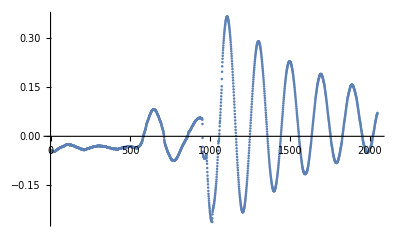

```mathematica
ListPlot[dataDriven]
```

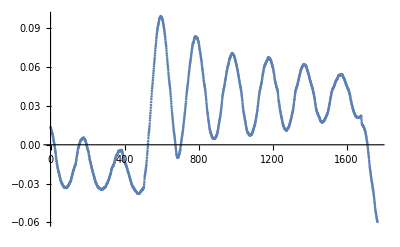

```mathematica
ListPlot[dataTrial1CounterClockwise]
```

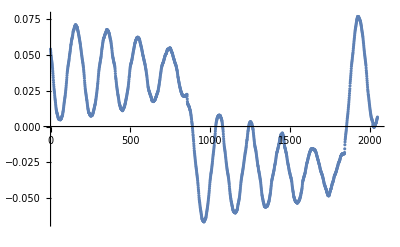

```mathematica
ListPlot[dataTrial1Clockwise]
```

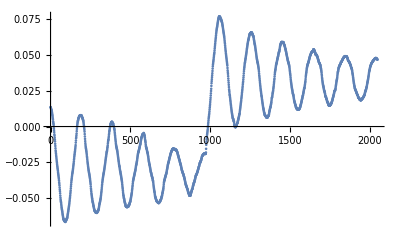

```mathematica
ListPlot[dataTrial2CounterClockwise]
```

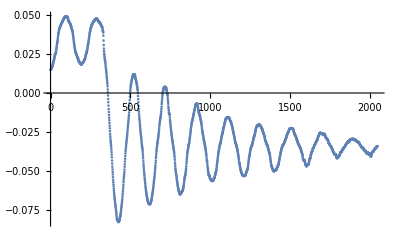

```mathematica
ListPlot[dataTrial2Clockwise]
```

## Trim the Data

```mathematica
(* Next we will cut the data sets to only incorporate the relevant sections of data *)
```

```mathematica
(* Just a test *)
```

```mathematica
dataDriven=Drop[dataDriven,975];
dataTrial1CounterClockwise=Part[dataTrial1CounterClockwise,500;;1650];
dataTrial1Clockwise=Part[dataTrial1Clockwise,855;;1800];
dataTrial2CounterClockwise=Drop[dataTrial2CounterClockwise,970];
dataTrial2Clockwise=Drop[dataTrial2Clockwise,350];
```

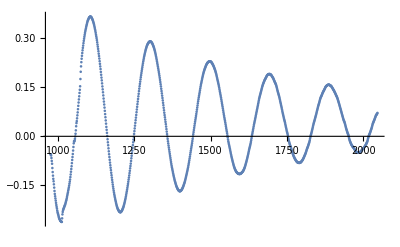

```mathematica
ListPlot[dataDriven]
```

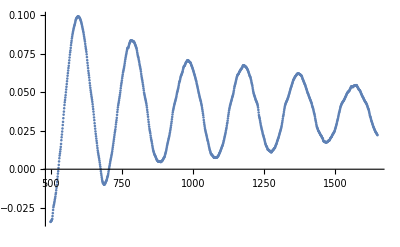

```mathematica
ListPlot[dataTrial1CounterClockwise]
```

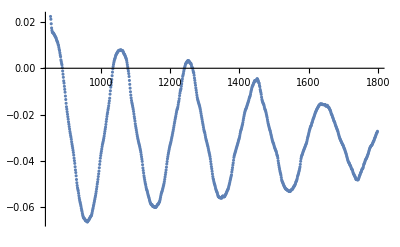

```mathematica
ListPlot[dataTrial1Clockwise]
```

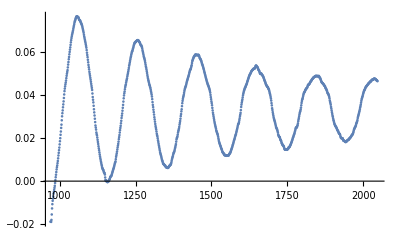

```mathematica
ListPlot[dataTrial2CounterClockwise]
```

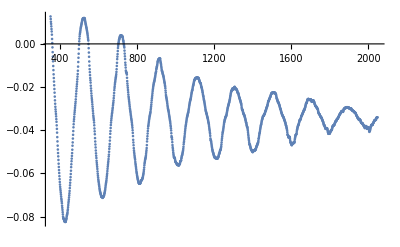

```mathematica
ListPlot[dataTrial2Clockwise]
```

## Fit the Data